```mathematica
(*Quit[]*)
```

# Exporting figures and tables for presentation

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
Clear[SaveFig];
Options[SaveFig]={Save->True};
SaveFig[name_, plot_, OptionsPattern[]]:=Module[{fileName="../TeX/presentation/figs/"<>name<>".pdf"},
If[OptionValue[Save],
Print["Saving figure to ", fileName];
Export[fileName, plot],
Print["Saving disabled"]
]
]
```

```mathematica
<<"mdat/ebert_ff.mdat";
<<"mdat/wang_ff.mdat";
<<"mdat/numbers.mdat";
<<"./mdat/amps.mdat";
<<"./mdat/branchings.mdat";
```

## Form Factors

### ff corrections

```mathematica
chiList={"chi_c0","chi_c1", "chi_c2"};
```

```mathematica
Table[{out,
rat=NIntegrate[100Ngamma[out,"enu", ffFitRule]/gammaTot,{q2, 0, q2Max[out]}]/$BR[out, "enu", "Ebert"];
1/√rat
}
,{out, chiList}]
```

(chi_c0 | 1.00006
chi_c1 | 1.00975
chi_c2 | 1.00928)

```mathematica
Table[{out,
rat=NIntegrate[100Ngamma[out,"enu", ffFitRule$Wang]/gammaTot,{q2, 0, q2Max[out]}]/$BR[out, "enu", "Wang"];
1/√rat
}
,{out, chiList}]
```

(chi_c0 | 1.00006
chi_c1 | 1.00099
chi_c2 | 0.999965)

### plots

```mathematica
Clear[genFFplot];
Options[genFFplot]={Factors->{1,1}};
genFFplot[func_,name_, out_, OptionsPattern[]]:=Module[{factors=OptionValue[Factors]},
Plot[
{factors⟦1⟧func[q2]/.ffFitRule,factors⟦2⟧func[q2]/.ffFitRule$Wang},
{q2, 0, q2Max[out]},
Frame->True,
FrameLabel->{"q^2, GeV^2", name<>"(q^2)"}, AxesOrigin->{0,0},
GridLines->Automatic
]
]
```

chi_c0

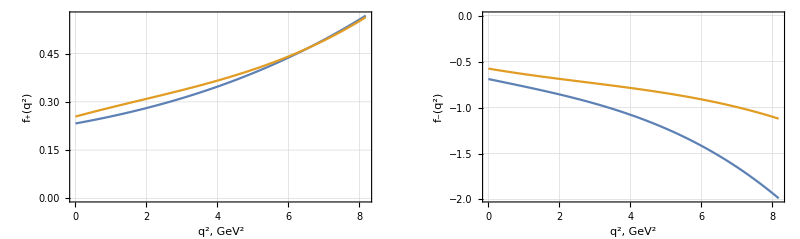

Saving figure to ../TeX/presentation/figs/ff_chi_c0.pdf

```mathematica
out = "chi_c0"
plt = Show[
GraphicsGrid[{{
genFFplot[fPlus, "f_+",out, Factors->{1,-1}],
genFFplot[fMinus, "f_-",out, Factors->{1,-1}]
}}]
, PlotLabel->"B_c→χ_c0W"]
SaveFig["ff_"<>out, plt];
```

chi_c1

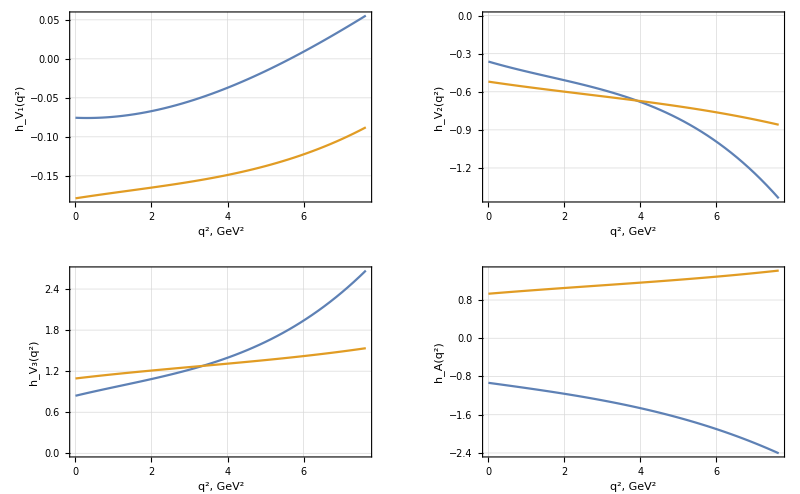

Saving figure to ../TeX/presentation/figs/ff_chi_c1.pdf

```mathematica
out="chi_c1"
plt = GraphicsGrid[{
{genFFplot[hV1,"h_V_1", out], genFFplot[hV2,"h_V_2", out]},
{genFFplot[hV3,"h_V_3", out], genFFplot[hA,"h_A", out]}
}]
SaveFig["ff_"<>out, plt];
```

chi_c2

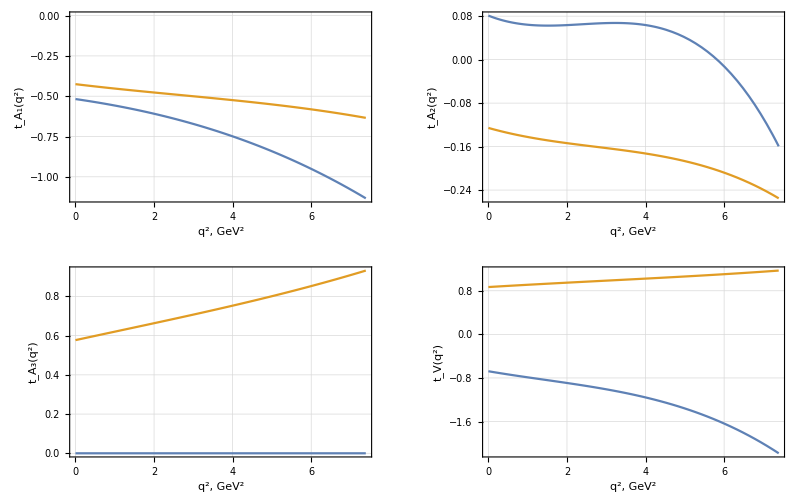

Saving figure to ../TeX/presentation/figs/ff_chi_c2.pdf

```mathematica
out="chi_c2"
plt = GraphicsGrid[{
{genFFplot[tA1,"t_A_1", out], genFFplot[tA2,"t_A_2", out]},
{genFFplot[tA3,"t_A_3", out], genFFplot[tV,"t_V", out]}
}]
SaveFig["ff_"<>out, plt];
```

## e nu

```mathematica
outL="enu"
```

enu

```mathematica
Clear[genEnuPlot];
Options[genEnuPlot]={Factors->{1,1}};
genEnuPlot[out_, OptionsPattern[]]:=Module[{factors=OptionValue[Factors]},
Plot[
{100Ngamma[out, "enu", ffFitRule]/gammaTot/BR[out,"enu","Ebert"],
100Ngamma[out, "enu", ffFitRule$Wang]/gammaTot/BR[out,"enu","Wang"]
},
{q2, 0, q2Max[out]},
Frame->True,
FrameLabel->{"q^2, GeV^2", "Γ^-1ⅆΓ/ⅆq^2"}, AxesOrigin->{0,0},
GridLines->Automatic,
PlotLegends->Placed[{"Ebert","Wang"}, Above]
]
]
```

### χ_c0

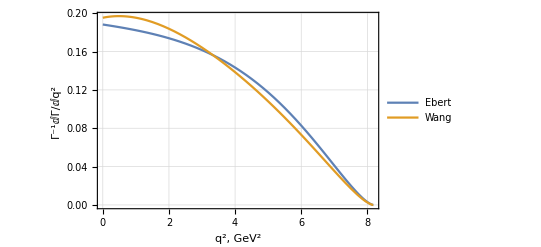

Saving figure to ../TeX/presentation/figs/enu_chi_c0.pdf

../TeX/presentation/figs/enu_chi_c0.pdf

```mathematica
out = "chi_c0";
plot = genEnuPlot[out]
SaveFig["enu_"<>out, plot]
```

```mathematica
{BR[out, outL,"Ebert"], $BR[out, outL,"Ebert"], BR[out, outL,"Wang"], $BR[out, outL,"Wang"]}
```

{0.15707,0.16,0.0700048,0.07}

### χ_c1

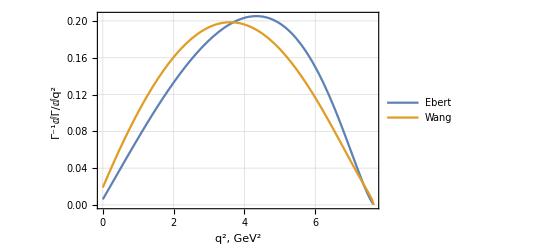

Saving figure to ../TeX/presentation/figs/enu_chi_c1.pdf

../TeX/presentation/figs/enu_chi_c1.pdf

```mathematica
out = "chi_c1";
plol = genEnuPlot[out]
SaveFig["enu_"<>out, plot]
```

### χ_c2

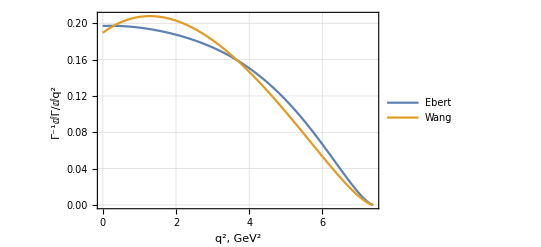

Saving figure to ../TeX/presentation/figs/enu_chi_c2.pdf

../TeX/presentation/figs/enu_chi_c2.pdf

```mathematica
out = "chi_c2";
plol = genEnuPlot[out]
SaveFig["enu_"<>out, plot]
```